# Visualizing Normalization

## A graphical presentation of NMR normalization methods.

Eric Moyer

Started 27 May 2012

## Introduction

Normalization methods in NMR spectrography (and probably other spectrographic fields as well) are typically explained by the procedures that you go through to perform them and justified by arguments about the "real concentration." Another way to look at normalization methods is to examine them as geometric operations on a vector space. This gives a different understanding of what is occurring, which can give the practitioner a deeper intuition about trade-offs he makes when he says, "sum-normalize the data."

I look at each spectrum generated as a point in a vector space, one variable in the vector for each value measured. I am mainly concerned with frequency-domain spectra, since it is on these that the normalization methods I present are typically used. The normalization methods do not solve extant problems on time-domain spectra, so they are not used there. However, my points are just as valid for time-domain spectra, since they too are vectors.

## Sum Normalization

Sum normalization takes each spectrum, divides it by its sum, and then multiplies it by a constant. After this operation, all spectra have the same sum.

If the spectra are interpreted as points in an n-dimensional vector space, this projects all points onto an n-1 dimensional subspace (hyperplane) along a line between the original point and the origin. In 3 dimensions, it projects points onto a the plane x+y+z=s . In 2 dimensions, all points are projected the line y=s-x. The location of these figures is determined by the constant.

How can we see this?

First, consider that multiplying a (non-zero) point by a constant moves it along a line connecting the point with the origin. Multiplying by a positive number less than 1 moves it closer to the origin. Multiplying by a number greater than 1 moves farther from the origin. And multiplying it by a negative number moves it away from the origin on the opposite side.

```mathematica
xPlusYEq1TwoD=Plot[{1-x},{x,-1,2},PlotStyle->Red];
```

```mathematica
yEq2X=Plot[{2x},{x,0,3/2},PlotStyle->Darker[Blue]];
```

```mathematica
ptX3HalvesY3AndProjection=ListPlot[{{{3/2,3}},{{1/3,2/3}}},PlotMarkers->{Automatic,Medium},PlotStyle->{Darker[Blue],Darker[Magenta]}];
```

```mathematica
firstDiagram=Show[{xPlusYEq1TwoD,Graphics[{Text["Constant sum surface",{0.6,0.5},{-1,0},BaseStyle->{Red}],Text["Spectrum",{3/2,11/4},{-1,0},BaseStyle->{Darker[Blue]}]}],yEq2X,ptX3HalvesY3AndProjection},PlotRange->All,AspectRatio->Automatic,ImageSize->{300},PlotRangeClipping->False];
```

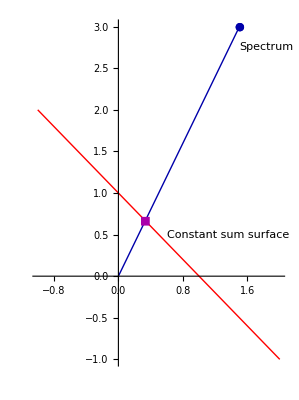
-Graphics-Figure 1: Sum Normalization in Two Dimensions

```mathematica
firstDiagramWithCaption=Labeled[firstDiagram,"Figure 1: Sum Normalization in Two Dimensions",Bottom,LabelStyle->Directive[Bold,FontFamily->Times]]
```

The point at which the line through the origin intersects with the surface of points whose sum equals the target sum of the sum-normalization is the normalized point. Figures 1 and 2 show sum-normalization in two and three dimensions with a target sum of 1.

```mathematica
sumEq1ThreeD=Graphics3D[{Opacity[0.85],Red,Polygon[{{-1,-1,3},{1,-1,1},{1,1,-1},{-1,1,1}}]},Axes->True];
```

```mathematica
yEq2XThreeD=Graphics3D[{Darker[Blue],Line[{{0,0,0},{3/2,0,3}}],PointSize[Large],Point[{3/2,0,3}],Text["Origin",{0,0,0},{-1.2,0}],Darker[Magenta],Point[{1/3,0,2/3}]}];
```

```mathematica
secondDiagram=Show[{sumEq1ThreeD,yEq2XThreeD}];
```

```mathematica
secondDiagramWithCaption=Labeled[secondDiagram,"Figure 2: Sum Normalization in Three Dimensions",Bottom,LabelStyle->Directive[Bold,FontFamily->Times]]
```

-Graphics3D-Figure 2: Sum Normalization in Three Dimensions

## Probabilistic Quotient Normalization

Probabilistic Quotient Normalization (PQN) (Dieterle 2006) is a method that is more resistant to large fluctuations in parts of the spectrum due to factors other than dilution (such as treatments). Unlike sum-normalization, which normalizes each spectrum independently, PQN is designed to normalize several related spectra simultaneously, using their commonality to improve its estimates.

PQN starts with sum-normalization. Next, the spectra are binned to take care of small peak-shifts. Then a reference spectrum is created. The original paper mentions several methods of creating reference spectra. However, for simplicity, we will choose the method that takes the median spectrum of all the spectra being analyzed. Then, for each spectrum to be normalized, the reference spectrum is divided by it and the median of the quotients is selected as the normalization factor. Finally the spectra are multiplied by their respective normalization factors.

For the following discussion, we will assume that the initial spectra have no negative values. Negative values result from noise or special acquisition methods like dephasing the water signal and should be removed during preprocessing. Though PQN is well-defined with negative values, their inclusion unnecessarily complicates the explanation.

### 2D PQN (the canonical way)

#### Sum Normalize

The first step of PQN we've seen before, we sum-normalize. In the diagrams, I sum-normalize to 1, since it is easy, but everything works out the same, just scaled a bit differently if you sum-normalize to a different constant.

```mathematica
orig2D={{2.172454345958343,1.7744919345405104},{2.675301724350803,1.359406145521423},{2.87830990460933,1.4709889319173473},{2.8813454193984884,1.073276896492814},{2.3606473361385762,1.7882842580601983},{2.26005835257858,1.7655977040112563},{1.398151988227432,2.097238014713233},{3.0861624358478528,0.9274842729247682},{2.255768229218814,1.8706253682049265},{2.6917625635090703,1.2898265639379862}};
```

```mathematica
sumNorm2D=Map[#/Total[#]&,orig2D];
```

```mathematica
thirdDiagram=Graphics[{PointSize->Medium,Darker[Blue],Map[Point[#]&,orig2D],Map[Line[{{0,0},#}]&,orig2D],Darker[Magenta],Map[Point[#]&,sumNorm2D],Red,Line[{{1,0},{0,1}}]},Axes->True];
```

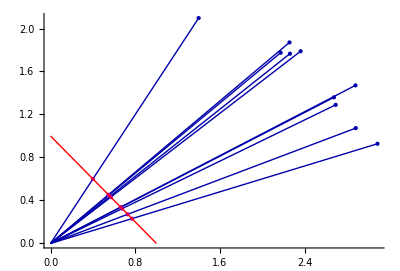
-Graphics-Figure 3: First step of 2D PQN: Sum-Normalize

```mathematica
thirdDiagramWithCaption=Labeled[thirdDiagram,"Figure 3: First step of 2D PQN: Sum-Normalize",Bottom,LabelStyle->Directive[Bold,FontFamily->Times]]
```

#### Reference Spectrum

Next, you generate a reference spectrum by taking the median of each variable.

```mathematica
refPt2D=Map[Median,Transpose[sumNorm2D]]
```

{0.615382,0.384618}

```mathematica
fourthDiagram=Graphics[{PointSize[Medium],Darker[Magenta],Map[Point[#]&,sumNorm2D],Red,Line[{{1,0},{0,1}}],Green,PointSize[Large],Point[refPt2D],Text["Reference spectrum",{0.025,0}+refPt2D,{-1,0}]},Axes->True];
```

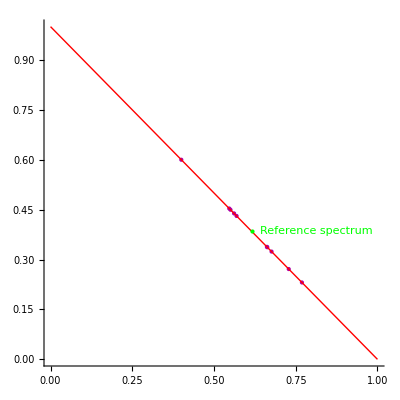
-Graphics-Figure 4: Second step of 2D PQN: Create reference spectrum

```mathematica
fourthDiagramWithCaption=Labeled[fourthDiagram,"Figure 4: Second step of 2D PQN: Create reference spectrum",Bottom,LabelStyle->Directive[Bold,FontFamily->Times]]
```

#### Reciprocal Quotient Spectra

In the next step, I make a change to the procedure that makes it easier to understand. Rather than dividing the reference spectrum by each of the individual spectra to get the quotient spectra, I divide each spectrum by the reference spectrum. This leaves me with quotient spectra that have the reciprocals of the proper coordinates. Because all of the individual coordinates are positive, this just reverses their ranks. The median element will still be the same. So, I can just divide by the median rather than multiplying to get the same final normalization. In the case of an even number of points, you can't get the reciprocal of the average by taking the average of the reciprocals. Thus, if the center two reciprocal quotients are a and b the reciprocal quotient median is m=(2a b)/(a+b)

```mathematica
standardQuotientTransformPlot=ParametricPlot[{{t,1-t},{refPt2D[[1]]/t,refPt2D[[2]]/(1-t)}},{t,0.001,1},AspectRatio->Automatic,PlotRange->{{0,3},{0,3}},ColorFunction->Function[{x,y,u},Hue[u/1.1]],PlotStyle->Thickness[0.025]];
```

```mathematica
standardQuotientArrows=Graphics[{Thickness[Small],Flatten[Map[{Hue[#],Arrow[{{#,1-#},{refPt2D[[1]]/#,refPt2D[[2]]/(1-#)}},{0,.9Abs[refPt2D[[1]]-#]}]}&,refPt2D[[1]]+{-0.15,-0.06,0.06,0.15}]]}];
```

```mathematica
fifthDiagram=Show[{standardQuotientTransformPlot,standardQuotientArrows,Graphics[{Text["Sum-normalized spectra",{1,0.2},{-1,0}],Text["Quotient spectra using standard method",{.9,2.5},{-1,0}],Text["Colors give correspondence (note reversal)",{0.9,2.36},{-1,0}] }]}];
```

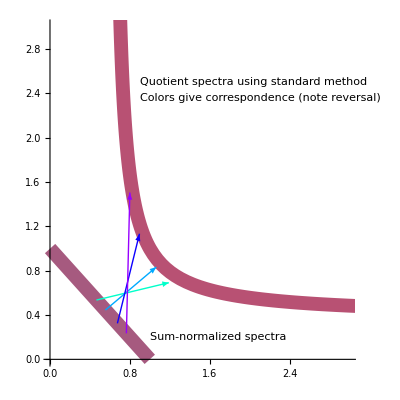
-Graphics-Figure 5: Standard method of creating quotient spectra

```mathematica
fifthDiagramWithCaption=Labeled[fifthDiagram,"Figure 5: Standard method of creating quotient spectra",Bottom,LabelStyle->Directive[Bold,FontFamily->Times]]
```

```mathematica
linearQuotientTransformPlot=ParametricPlot[{{t,1-t},{t/refPt2D[[1]],(1-t)/refPt2D[[2]]}},{t,0.001,1},AspectRatio->Automatic,PlotRange->{{0,3},{0,3}},ColorFunction->Function[{x,y,u},Hue[u/1.1]],PlotStyle->Thickness[0.025]];
```

```mathematica
linearQuotientArrows=Graphics[{Thickness[Small],Flatten[Map[{Hue[#],Arrow[{{#,1-#},{#/refPt2D[[1]],(1-#)/refPt2D[[2]]}},0.1]}&,refPt2D[[1]]+{-.25,-0.15,-0.06,0.06,0.15,0.25}]]}];
```

```mathematica
sixthDiagram=Show[{linearQuotientTransformPlot,linearQuotientArrows,Graphics[{Text["Sum-normalized",{1.1,0.1},{-1,0}],Text["Reciprocal Quotient spectra",{0.4,2.29},{-1,0}],Text["Colors give correspondence",{0.4,2.15},{-1,0}] }]}];
```

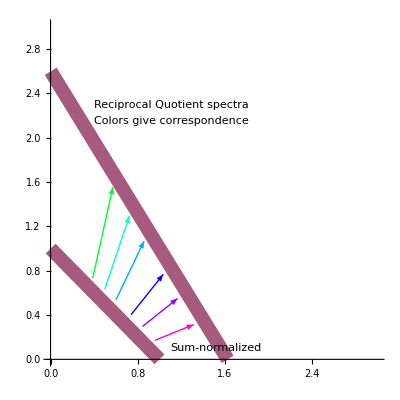
-Graphics-Figure 6: Easy-to-visualize method of creating reciprocal quotient spectra

```mathematica
sixthDiagramWithCaption=Labeled[sixthDiagram,"Figure 6: Easy-to-visualize method of creating reciprocal quotient spectra",Bottom,LabelStyle->Directive[Bold,FontFamily->Times]]
```

The standard method involves three non-linear transformations of the spectral space, one to create the quotient spectra and then another to extract their medians, and a third to multiply the corresponding spectra by their medians. My method involves only two non-linear transformations - extracting the medians and dividing by them. The creation of the reciprocal quotient  (r-quotient) spectra is a linear transformation. Further, my method of creating the quotients does not flip the axes. This makes my method much easier to visualize. You can compare the two methods of creating the quotient spectra by looking at figures 5 and 6 (these diagrams are created using the reference spectrum from figure 4).

#### Median Reciprocal Quotients

After generating the r-quotient spectra, the next step is to take the median of the r-quotients, that is, the median of all of the coordinates of each spectrum. The r-quotient spectra lie on the line between (1/r,0) and (0,1/(1-r)). This line is y=r/(r-1)x+1/(1-r). Applying the reciprocal median formula above to the points on the r-quotient  line (q, r/(r-1)q+1/(1-r)) we get m=2 q (1-r q)/(1+q-2 r q).

```mathematica
rMedianAndRQuotientCurve=With[{r=refPt2D[[1]]},ParametricPlot[{{q,(r q)/(r-1)+1/(1-r)},{q,(r q)/(r-1)+1/(1-r)}+((2q(1-r q))/(1+q-2r q))quotientLineUnitNormal},{q,0,1/r}]];
```

```mathematica
Module[{rqpt,r},
r=refPt2D[[1]];
rqpt[q_]:={{q,(r q)/(r-1)+1/(1-r)},{q,(r q)/(r-1)+1/(1-r)}+((2q(1-r q))/(1+q-2r q))quotientLineUnitNormal};
rMedianRQuotientArrows=Graphics[{Blue,Map[Arrow[rqpt[#]]&,1/refPt2D[[1]]{0.125,0.25,0.375,0.5,0.625,0.75,0.875}]}]
];
```

```mathematica
quotientLineLeftEndpoint={0,1/refPt2D[[2]]};
```

```mathematica
quotientLineRightEndpoint={1/refPt2D[[1]],0};
```

```mathematica
quotientLineUnitNormal=Reverse[Normalize[quotientLineRightEndpoint-quotientLineLeftEndpoint]]{-1,1};
```

```mathematica
seventhDiagram=Show[rMedianAndRQuotientCurve,rMedianRQuotientArrows];
```

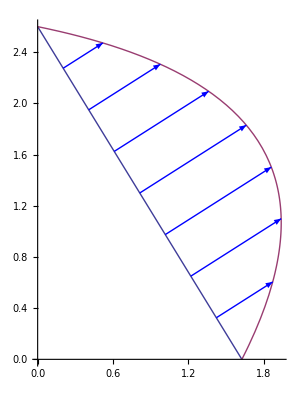
-Graphics-Figure 7: Median r-quotient as distance perpendicular to r-quotient line.

```mathematica
seventhDiagramWithCaption=Labeled[seventhDiagram,"Figure 7: Median r-quotient as distance perpendicular to r-quotient line. ",Bottom,LabelStyle->Directive[Bold,FontFamily->Times]]
```

#### Move Median R-Quotients

The median r-quotients in the previous step are displayed attached to their corresponding reciprocal quotient points. But they should be attached to the sum-normalized points. The next step matches the median quotients back to the original points. Substituting q=x/r into the median equation above yields m=(2 (1-x) x)/(r+x-2 r x)=(2x (1-x))/(r(1-x)+x(1-r))=(2x y)/(x(1-r)+y r)

```mathematica
FullSimplify[Solve[{m==(2q(1-r q))/(1+q-2r q),q==x/r},{m},{q}]]
```

```mathematica
{{m->(2 (1-x) x)/(r+x-2 r x)}}
```

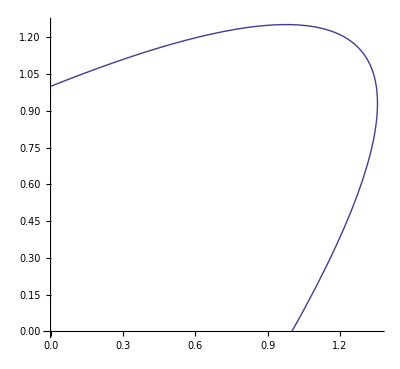

```mathematica
sumNormAppropriateMedianCurve=With[{r=refPt2D[[1]]},ParametricPlot[{x,1-x}+(2 (1-x) x)/(r+x-2 r x)Normalize[{1,1}],{x,0,1}]]
```

```mathematica
sumNormPointsPlot=Graphics[{PointSize[Medium],Darker[Magenta],Map[Point[#]&,sumNorm2D],Red,Line[{{1,0},{0,1}}]},Axes->True];
```

```mathematica
ninthDiagram=Show[sumNormAppropriateMedianCurve,sumNormPointsPlot,Options[sumNormPointsPlot]];
```

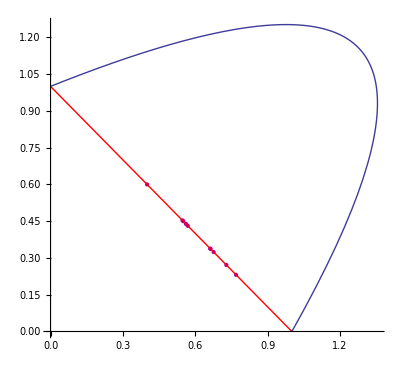
-Graphics-Figure 9: Sum-normalized points with their r-quotient scaling factors above them.

```mathematica
ninthDiagramWithCaption=Labeled[ninthDiagram,"Figure 9: Sum-normalized points with their r-quotient scaling factors above them.",Bottom,LabelStyle->Directive[Bold,FontFamily->Times]]
```

#### Scale Sum-Normalized Points

The final step is to divide each spectrum by its corresponding reciprocal quotient. This results in the curve y=((-1+r) x)/(r-2 x) on the interval [r/2,∞). (Note that there is a y asymptote as well aty=(1-r)/2). Letting (R_x,R_y) be the coordinates of the reference point, this curve is the hyperbola x y =R_x/2 R_y/2 with the origin translated to  (R_x/2,R_y/2) . The scaled spectra are the intersections of this curve with the lines connecting the original points and the origin.

```mathematica
originToPoints2D=Graphics[{PointSize->Medium,Darker[Blue],Map[Point[#]&,orig2D],Map[Line[{{0,0},#}]&,orig2D]},Axes->True];
```

```mathematica
finalScalingPlot2D=With[{r=refPt2D[[1]]},Plot[((-1+r) x)/(r-2 x),{x,r/2+0.0001,3},PlotRange->{{0,3},{0,2.5}},PlotStyle->Orange,AspectRatio->Automatic]];
```

```mathematica
scaledPoints2DPlot=Graphics[{Darker[Darker[Orange]],PointSize[Medium],Point[With[{r=refPt2D[[1]]},Map[Function[t,{t/((2 (1-t) t)/(r+t-2 r t)),(1-t)/((2 (1-t) t)/(r+t-2 r t))}],Transpose[sumNorm2D][[1]]]
]]}];
```

```mathematica
tenthDiagram=Show[{originToPoints2D,finalScalingPlot2D,scaledPoints2DPlot},AspectRatio->Automatic];
```

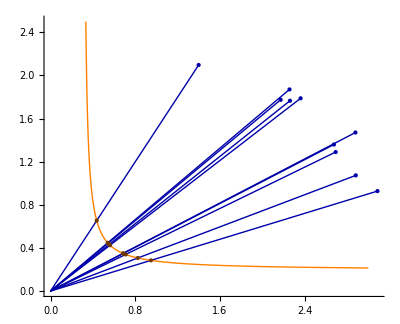
-Graphics-Figure 10: Final scaling of points based on generated median quotients.

```mathematica
tenthDiagramWithCaption=Labeled[tenthDiagram,"Figure 10: Final scaling of points based on generated median quotients.",Bottom,LabelStyle->Directive[Bold,FontFamily->Times]]
```

##### Work deriving equations

```mathematica
Simplify[Solve[{x==t/((2 (1-t) t)/(r+t-2 r t)),y==(1-t)/((2 (1-t) t)/(r+t-2 r t))},{y},{t}]]
```

{{y→((-1+r) x)/(r-2 x)}}

```mathematica
Simplify[t/((2 (1-t) t)/(r+t-2 r t))]
```

(r+t-2 r t)/(2-2 t)

```mathematica
Solve[x==(r+t-2 r t)/(2-2 t),{t}]
```

{{t→(r-2 x)/(-1+2 r-2 x)}}

```mathematica
y==(1-t)/((2 (1-t) t)/(r+t-2 r t))/.{{t->(r-2 x)/(-1+2 r-2 x)}}
```

{y==((r+(r-2 x)/(-1+2 r-2 x)-(2 r (r-2 x))/(-1+2 r-2 x)) (-1+2 r-2 x))/(2 (r-2 x))}

```mathematica
FullSimplify[y==((r+(r-2 x)/(-1+2 r-2 x)-(2 r (r-2 x))/(-1+2 r-2 x)) (-1+2 r-2 x))/(2 (r-2 x))]
```

((-1+r) x)/(r-2 x)==y

```mathematica
refPt2D/2
```

{0.307691,0.192309}

```mathematica
Simplify[{t,1-t}/((2 (1-t) t)/(r+t-2 r t))]
```

{(r+t-2 r t)/(2-2 t),(r+t-2 r t)/(2 t)}

```mathematica
{(r+t-2 r t)/(2-2 t),(r+t-2 r t)/(2 t)}/.t->Subscript[x, sn]
```

{(r+x_sn-2 r x_sn)/(2-2 x_sn),(r+x_sn-2 r x_sn)/(2 x_sn)}

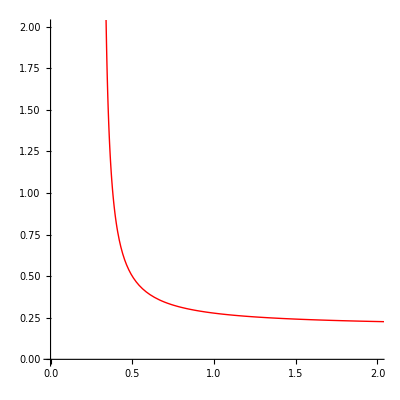

```mathematica
bar=With[{r=refPt2D[[1]]},ParametricPlot[{(r+t-2 r t)/(2-2 t),(r+t-2 r t)/(2 t)},{t,0.01,0.99},PlotRange->{{0,2},{0,2}},AspectRatio->Automatic,PlotStyle->Red]]
```

```mathematica
Limit[(r+t-2 r t)/(2-2 t),t->0](*X asymptote*)
```

r/2

```mathematica
Limit[(r+t-2 r t)/(2 t),t->1](*Y asymptote*)
```

(1-r)/2

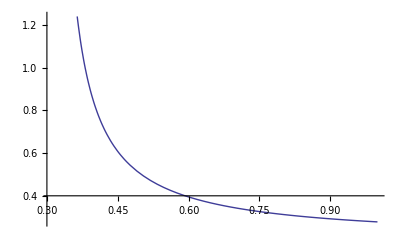

```mathematica
foo=With[{r=refPt2D[[1]]},Plot[((-1+r) x)/(r-2 x),{x,r/2,1}]]
```

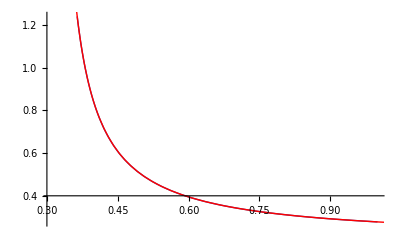

```mathematica
Show[{foo,bar}]
```

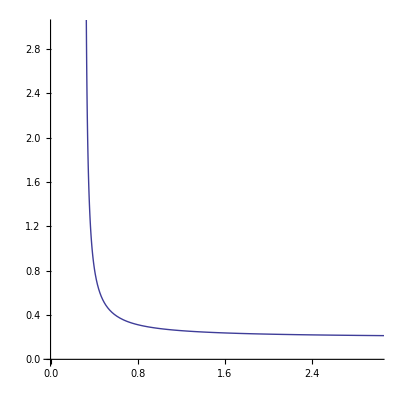

```mathematica
medianScaledSumNorm=With[{r=refPt2D[[1]]},ParametricPlot[{t,1-t}/((2 (1-t) t)/(r+t-2 r t)),{t,0.01,0.99},PlotRange->{{0,3},{0,3}}]]
```

Find all equations that match what we know so far about the eventual function: its asymptotes are the two axis-parallel lines through refPt/2 (the two limit expressions) and it is a hyperbola (the long equation and inequality). Looks like I was wrong and it is not a hyperbola. The conditions only hold if x and y are constant functions of r. (Later, it is obvious it is a hyperbola, I don't know where I went wrong here.)

```mathematica
Reduce[a x^2+b x y+c y^2+d x+e y+f==0&&b^2>4a c &&Limit[y,x->Infinity]==(1-r)/2&&Limit[x,y->Infinity]==r/2&&0<r<1&&x>=r/2&&y>=(1-r)/2,{y},Reals]
```

((c<0&&0<x<1/2&&f<1/(4 c)(-c^2-2 c e-2 b c x+4 c^2 x-4 c d x+4 c e x-b^2 x^2+4 b c x^2-4 c^2 x^2))||(c==0&&((b<0&&0<x<1/2)||(b>0&&0<x<1/2)))||(c>0&&0<x<1/2&&f>1/(4 c)(-c^2-2 c e-2 b c x+4 c^2 x-4 c d x+4 c e x-b^2 x^2+4 b c x^2-4 c^2 x^2)))&&r==2 x&&a==1/x^2(-f-1/2 e (1-r)-1/4 c (1-r)^2-d x-1/2 b (1-r) x)&&y==(1-r)/2

```mathematica
Solve[y==((-1+r) x)/(r-2 x),{r}]
```

{{r→(x-2 x y)/(x-y)}}

```mathematica
FullSimplify[y+(1-r)(x+r/2)/(r-2(x+r/2))/.r->2b]
```

((-1+2 b) (b+x))/(2 x)+y

```mathematica
FullSimplify[Reduce[y-(1-r)(x+r/2)/2x==0&&0<r<1&&z==Limit[y,x->Infinity],{z},Reals]]
```

0<r<1&&(-1+r) x (r+2 x)+4 y==0&&y==z

```mathematica
Simplify[(1-r)(x+r/2)/(2x)-(1-r)/2]
```

-((-1+r) r)/(4 x)

```mathematica
Simplify[Solve[(x-r/2)(y-(1-r)/2)-(r/2)((1-r)/2)==0,{y}]]
```

{{y→((-1+r) x)/(r-2 x)}}

```mathematica
Times@@{2,3}
```

6

```mathematica
Sqrt[Times@@refPt2D/2]
```

0.344011

```mathematica
With[{r=refPt2D[[1]],foc=Sqrt[Times@@refPt2D/2]},Graphics[{PointSize[Large],Point[{foc,foc}]}]];
```

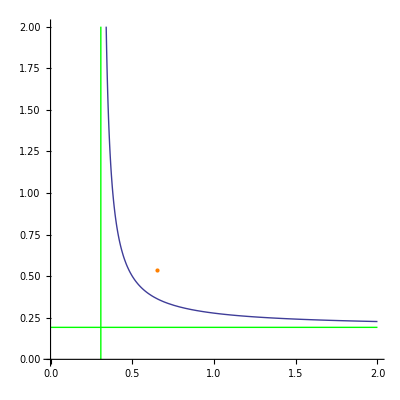

```mathematica
With[{r=refPt2D[[1]],untrFoc=Sqrt[Times@@refPt2D/2]},Show[{Plot[((-1+r) x)/(r-2 x),{x,r/2,2},PlotRange->{{0,2},{0,2}},AspectRatio->Automatic],Graphics[{Orange,PointSize[Large],Point[{untrFoc,untrFoc}+refPt2D/2],Green,Line[{{0,(1-r)/2},{2,(1-r)/2}}],Line[{{r/2,0},{r/2,2}}]}]
}]
]
```

```mathematica
rQuotientForX2D[x_,refPt_]:=With[{xQuot=x/refPt[[1]],yQuot=(1-x)/refPt[[2]]},
(xQuot+yQuot)/2]
```

##### A digression on the form of the reciprocal median quotient curve

There were two interesting characteristics of the median quotients. First, the median quotient is 1for exactly two spectra for any given reference spectrum. First, the reference spectrum is given a quotient of 1. Second (unless the reference spectrum has a 0) is the spectrum with all equal heights (normalized x=1/2) is also always unchanged for two dimensional spectra.

```mathematica
Simplify[Reduce[(2 (1-x) x)/(r+x-2 r x)==1&&0≤x≤1&&0≤r≤1,{x}]]
```

(r==x&&(0<r<1/2||1/2<r<1))||(2 x==1&&0≤r&&r≤1)

Second, the maximum reciprocal quotient is located along a lovely s-shaped curve.

```mathematica
Reduce[D[(2 (1-x) x)/(r+x-2 r x),x]==0&&0≤x≤1&&0≤r≤1,{x}]
```

(0<r<1/2&&x==r/(-1+2 r)+√((r-r^2)/(-1+2 r)^2))||(r==1/2&&x==1/2)||(1/2<r<1&&x==r/(-1+2 r)-√((r-r^2)/(-1+2 r)^2))

```mathematica
Reduce[D[(2 (1-x) x)/(r+x-2 r x),x]==0&&0≤x≤1&&0≤r≤1]
```

0<x<1&&r==x^2/(1-2 x+2 x^2)

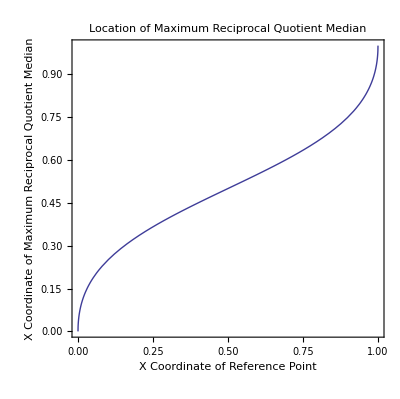

```mathematica
Plot[Which[0<r<1/2,r/(-1+2 r)+√((r-r^2)/(-1+2 r)^2),
r==1/2,1/2,1/2<r<1,r/(-1+2 r)-√((r-r^2)/(-1+2 r)^2)],{r,0,1},Frame->{True,True,False,False},AspectRatio->Automatic,FrameLabel->{"X Coordinate of Reference Point", "X Coordinate of Maximum Reciprocal Quotient Median"},PlotLabel->"Location of Maximum Reciprocal Quotient Median"]
```

### 2D PQN (the easy way)

Because 2D is such a special case (the median is the same as the mean and the reference spectrum can be specified by one variable), the entire normalization procedure can be viewed in three simple steps. First, sum normalize to half of the sum you would otherwise choose and choose the reference spectrum. This makes the reference spectrum r equal to r/2 in the original procedure.

Second, call the coordinates of our new refrence point R, we can then construct the hyperbola x y = R_x R_y on the coordinates system with R as the origin.

Finally, intersect the lines to our original spectra with this hyperbola to get the final, scaled spectra.

This whole procedure can be represented in one diagram.

```mathematica
twelfthDiagram=Show[{originToPoints2D,finalScalingPlot2D,scaledPoints2DPlot,Graphics[{
Red,Line[{{0.5,0},{0,0.5}}],
Text["sum=0.5",{0.5,0.15},{-1,1}],
Magenta,PointSize[Medium],
Map[Point[#/Total[2#]]&,orig2D],Green,Point[refPt2D/2],Dashed,Line[{{0,refPt2D[[2]]/2},{3,refPt2D[[2]]/2}}],Line[{{refPt2D[[1]]/2,0},{refPt2D[[1]]/2,2.5}}],Text["Reference point",{2.0,0.2},{-1,1}],Orange,Text["Hyperbola from",{0.4,2.1},{-1,1}],Text["reference point",{0.4,1.98},{-1,1}]
}]
},AspectRatio->Automatic];
```

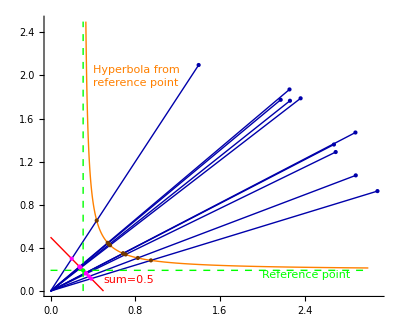
-Graphics-Figure 12: Probabilistic quotient normalization process in one diagram.

```mathematica
twelfthDiagramWithCaption=Labeled[twelfthDiagram,"Figure 12: Probabilistic quotient normalization process in one diagram.",Bottom,LabelStyle->Directive[Bold,FontFamily->Times]]
```

### 3D PQN

#### Sum-normalize

The PQN with 3D spectra starts out similar to 2D PQN. Figure 13 shows a group of spectra normalized to a constant sum of 1. I only show the first quadrant because of my earlier assumption that all points are positive.

```mathematica
Join[Table[{RandomReal[UniformDistribution[{1,2}]],RandomReal[UniformDistribution[{1,3}]],RandomReal[UniformDistribution[{1.2,1.3}]]},{8}],Table[{RandomReal[UniformDistribution[{1,2}]],RandomReal[UniformDistribution[{1,3}]],RandomReal[UniformDistribution[{0.3,0.4}]]},{8}]]/2
```

```mathematica
orig3D={{0.7887122746455992,1.370162229032098,0.6331315511805435},{0.7458987631156281,0.7715290755810482,0.6148123738797091},{0.657133266164412,0.9221468105687936,0.6040697246875196},{0.5857304644159957,0.5419021027040107,0.6173275066394556},{0.6919142797105331,1.4387362033967048,0.6247078566848845},{0.5457398713571942,0.8830657889311706,0.6314481246718616},{0.6175342173424286,0.7957609324327515,0.6258393391396256},{0.9921345376422709,0.690496919850571,0.6062680422006831},{0.5768632417698818,0.7497757265321776,0.19303894295071117},{0.5084130070212706,0.6455535679017173,0.17770724565742288},{0.552620580638311,1.0787269445880796,0.17767927573922487},{0.8527000484773908,0.7900375918166862,0.1618452370779209},{0.8558169686389362,0.8381051726099,0.19646170205328767},{0.9128626837404124,1.2855838089650504,0.1525320368241421},{0.5595750105400437,1.4879212199688876,0.19946889532440698},{0.6276434675023799,1.3262524986373982,0.1958156408376076}};
```

```mathematica
sumNorm3D=Map[#/Total[#]&,orig3D];
```

```mathematica
thirteenthDiagram=Graphics3D[{Blue,PointSize[Medium],Point[orig3D],Line[Map[{{0,0,0},#}&,orig3D]],Red,Opacity[0.85],Polygon[{{0,0,1},{0,1,0},{1,0,0}}],Magenta,Point[sumNorm3D]},Axes->True,AxesLabel->{x,y,z}];
```

```mathematica
thirteenthDiagramWithCaption=Labeled[thirteenthDiagram,"Figure 13: Sum-normalizing points in 3D.",Bottom,LabelStyle->Directive[Bold,FontFamily->Times]]
```

-Graphics-Figure 13: Sum-normalizing points in 3D.

#### Choose the reference

After sum-normalizing, you choose a reference spectrum. Note that, unlike the 2D case, the reference spectrum is not necessarily sum-normalized. Figure 14 shows one such case.

```mathematica
refPt3D=Median/@Transpose[sumNorm3D];
```

```mathematica
fourteenthDiagram=Graphics3D[{Red,Opacity[0.85],Polygon[{{0,0,1},{0,1,0},{1,0,0}}],Magenta,Point[sumNorm3D],Green,PointSize[Large],Point[refPt3D],Opacity[1],Line[{{0,refPt3D[[2]],refPt3D[[3]]},{1,refPt3D[[2]],refPt3D[[3]]}}],Line[{{refPt3D[[1]],0,refPt3D[[3]]},{refPt3D[[1]],1,refPt3D[[3]]}}],Line[{{refPt3D[[1]],refPt3D[[2]],0},{refPt3D[[1]],refPt3D[[2]],1}}]},Axes->True,AxesLabel->{x,y,z}];
```

```mathematica
fourteenthDiagramWithCaption=Labeled[fourteenthDiagram,"Figure 14: A reference spectrum that is not sum-normalized derived from sum-normalized spectra.",Bottom,LabelStyle->Directive[Bold,FontFamily->Times]]
```

-Graphics3D-Figure 14: A reference spectrum that is not sum-normalized derived from sum-normalized points.

#### Form the r-quotient plane and divide into median regions

Now, we form the reciprocal quotient plane from the sum-normalized plane by dividing all points by the reference spectrum, R. We assume that none of the coordinates of R is 0. This forms the plane (x,y,z)·R=1. Since we are in the first quadrant, the section of the plane we are interested in is a triangle. If we draw lines cooresponding to x=y ,x=z, and y=z, we will divide the triangle into 6 regions. On each of these regions, the median is one of the coordinates of the plane. These lines all intersect at x=y=z=1/(R_x+R_y+R_z), where the reciprocal median quotient is 1/(R_x+R_y+R_z). Along each line, the median is the value of the two equal coordinates. So, on the line x=y, the median is x or equivalently, y. Each region is bounded by two lines. The median in that region is the variable that is common to its two bounding lines. So, the median of the region bounded by x=y and x=z is x. If a and b are the coordinates of a line a==b and c is the non-included coordinate. The lines run from the corner where c is non-zero to the opposite edge where c=0 and a=b=1/(R_a+R_b).

```mathematica
Simplify[Reduce[0<rx<1&&0<ry<1&&t/(1-t)==rx/ry&&x==t/rx&&y==(1-t)/ry,{x,y,t,rx,ry},Reals]]
```

x==y&&((x>1&&0<t&&t<1)||(t+x>1&&2 x>1&&t<x&&x≤1))&&rx==t/x&&rx+ry==rx/t

```mathematica
Solve[t/(1-t)==rx/rz,{t}]
```

{{t→rx/(rx+rz)}}

```mathematica
rx/(rx+rz)/rx
```

1/(rx+rz)

```mathematica
Reduce[y==z&&x==y&&x rx+y ry+z rz==1,{x,y,z}]
```

rx+ry+rz≠0&&x==1/(rx+ry+rz)&&y==x&&z==x

```mathematica
Reduce[y==z&&x refPt3D[[1]]+y refPt3D[[2]]+z refPt3D[[3]]==1,{z,y}]
```

z==1.55244-0.497674 x&&y==1.55244-0.497674 x

```mathematica
f[x_]:=1.5524435203393163-0.4976740578487859 x
```

```mathematica
f[3]
```

0.0594213

```mathematica
fifteenthDiagram=Graphics3D[{Magenta,Opacity[0.85],Polygon[{{0,0,1}/refPt3D[[3]],{0,1,0}/refPt3D[[2]],{1,0,0}/refPt3D[[1]]}],Opacity[1],Yellow,With[{a=1/(refPt3D[[1]]+refPt3D[[2]]),c=1/refPt3D[[3]]},Line[{{a,a,0},{0,0,c}}]],With[{a=1/(refPt3D[[1]]+refPt3D[[3]]),c=1/refPt3D[[2]]},Line[{{a,0,a},{0,c,0}}]],With[{a=1/(refPt3D[[2]]+refPt3D[[3]]),c=1/refPt3D[[1]]},Line[{{0,a,a},{c,0,0}}]]},Axes->True,AxesLabel->{x,y,z},Lighting->"Neutral"];
```

```mathematica
fifteenthDiagramWithCaption=Labeled[fifteenthDiagram,"Figure 15: The r-quotient plane derived from figure 14 split into sections of uniform median coordinate.",Bottom,LabelStyle->Directive[Bold,FontFamily->Times]]
```

-Graphics3D-Figure 15: The r-quotient plane derived from figure 14 split into sections of uniform median coordinate.